```mathematica
<<AceFEM`;
```

Setup the domain as used while generating the dataset.

```mathematica
L=4;H=1;
points={{0,0},{L,0},{L,H},{0,H}};
SMTInputData[];
SMTAddDomain[{"Ω",{"ML:","SE","PE","T1","DF","HY","T1","D",{{"NeoHooke","WA"}}},{"E *"->500,"ν *"->0.3}}];mesh=ToElementMesh[ImplicitRegion[(x-3)^2+(y-0.5)^2>0.1,{x,y}],{{0,L},{0,H}},"MeshOrder"->1,MaxCellMeasure->1];SMTAddMesh[mesh,"Ω"];
SMTAddEssentialBoundary["X"==0&,1->0,2->0];
SMTAnalysis[];
mrest = SMTShowMesh["BoundaryConditions"-> False, "FillElements"->False,"Mesh"->Gray, "ImageSize"->200];
```

Import the prediction file to be visualized.

```mathematica
input = Import["examples/2dholemagnet.csv"];
nn=input[[All,2]] ;
fem = input[[All,3]] ;
error = input[[All,4]];
listerror = Partition[error, 2];
nodeerror = (Norm/@listerror);
```

Visualise FEM and NN Predictions

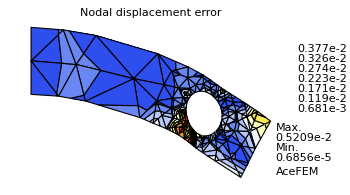
-Graphics- -Graphics-

```mathematica
(*Assign true FEM solutions. Red mesh*)
SMTNodeData["at",Partition[fem ,2]];
mfem=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Red,"FillElements"->False,"ImageSize"->300];

(*Assign neural network predictions. Blue mesh*)
SMTNodeData["at",Partition[nn ,2]];
mnn=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Blue,"FillElements"->False,"ImageSize"->300];

(*Plot prediction error*)
errorplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> nodeerror,"Contour"->True,"ImageSize"->350,"Label"-> "Nodal displacement error"] ;

Show[mfem,mnn,mrest]  Show[errorplt]
```

Von Mises Prediction for FEM and MAgNET

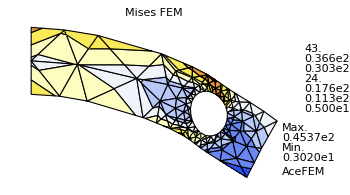
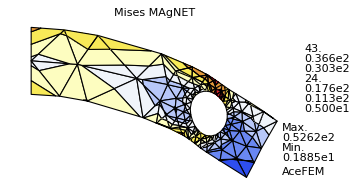

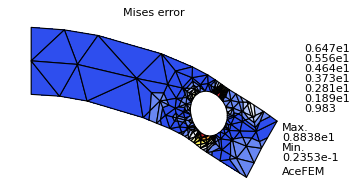

```mathematica
(*Von mises plot for the FEM solution*)
SMTNodeData["at",Partition[fem ,2]];
misesfem = SMTPostData["Mises stress"];
femmisesplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> misesfem,"Contour"->{5,43,5},"ImageSize"->350, "Label"-> "Mises FEM"] ;

(*Von mises plot for the NN solution*)
SMTNodeData["at",Partition[nn ,2]];
misesnn = SMTPostData["Mises stress"];
nnmisesplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> misesnn ,"Contour"->{5,43,5},"ImageSize"->350,"Label"-> "Mises MAgNET"] ;

(*Von mises prediction error*)
errormises = Abs[misesnn- misesfem];
misesplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> errormises,"Contour"->True,"ImageSize"->350, "Label"-> "Mises error"] ;

Show[femmisesplt]Show[nnmisesplt]
Show[misesplt]
```

Computing residual forces in the domain for MAgNET prediction

Point force applied = {1.28051,-4.43340}

% realtive error in retrieving residuals at the fixed boundary = 4.79708

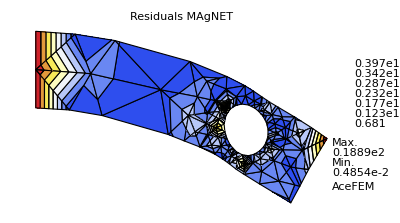

```mathematica
(*Get the value of externally applied point load*) 
pointforce = input[[All,1]];  
noninds = Flatten[SparseArray[pointforce]["NonzeroPositions"]];
externalload = pointforce[[noninds]];(*Round of the force value*)
Print["Point force applied = ",NumberForm[externalload,6]];

(*Compute the residuals at the fixed boundary*)
boundaryresidual = Total[SMTResidual[Line[{{0,0},{0,H}}]]] ;
(* In the ideal case, boundaryresidual = -1 x externalload *) 
Relerror = (Norm[externalload]- Norm[boundaryresidual])*100/Norm[externalload];

Print["% realtive error in retrieving residuals at the fixed boundary = ", Relerror]

(*Plot the residual forces*)
noderesidual = SMTResidual[Point[SMTNodeData["X"]]];
noderesidual = (Norm/@noderesidual);
resplt=SMTShowMesh["BoundaryConditions"->False,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> noderesidual,"Contour"->True,"ImageSize"->400,"Label"-> "Residuals MAgNET"] ;
Show[resplt]
```